## Undamped oscillator (Example 5.8: “Euler vs. Tustin”)

```mathematica
Clear["Global`*"];
SetOptions[ListPlot,Joined->True,InterpolationOrder->0,PlotRange -> All];
SetOptions[Plot,PlotRange -> All];

(*Ts=0.1; *)  Ts=0.22;  (* choose different time steps *)
Ts=0.1;
tmax=18Ts; tmaxu=9 Ts;PulseInput=UnitStep[t] UnitStep[Ts-t]/Ts; DiscreteImpulse=DiscreteDelta[t]/Ts;
```

First, the continuous case, using a modified PD control

```mathematica
G1=1/(s^2+1); (* S1=1/(G1(2+s)^2);  K1=Together[1/G1 T1/S1]; *)

K1 = (3+4s)/(1+s/10);
S1=Together[1/(1+K1 G1)];T1=Together[1-S1]; 
GS1=Together[G1 S1]; KS1=Together[K1 S1];

G1tf=TransferFunctionModel[G1,s] ;   (* continuous, stable osc. *)
T1tf=TransferFunctionModel[T1,s];
K1tf=TransferFunctionModel[K1,s];
GS1tf=TransferFunctionModel[GS1,s];  (* sys response to input disturbance *)
KS1tf=TransferFunctionModel[KS1,s];

y0=OutputResponse[G1tf,PulseInput,{t,0,tmax}](* input to open-loop sys *);
y1=OutputResponse[GS1tf,PulseInput,{t,0,tmax}]; (* input disturb. *)
u1=-OutputResponse[T1tf,PulseInput,{t,0,tmaxu}];
y1r=OutputResponse[T1tf,UnitStep[t],{t,0,tmax}];     (* sys to command step *)
u1r=OutputResponse[KS1tf,UnitStep[t],{t,0,tmaxu}][[1]]; 

py0=Plot[y0,{t,0,tmax},PlotStyle ->{Thick,Red}];
py1=Plot[y1,{t,0,tmax},PlotStyle ->{Thick,Black}];
py1r=Plot[y1r,{t,0,tmax},PlotStyle ->{Thick,Black}];
pu1=Plot[u1,{t,0,tmaxu},PlotStyle ->{Thick,Black}];
puin=Plot[PulseInput,{t,0,tmaxu},PlotStyle ->{White}, Filling->Bottom];
pu1r=Plot[u1r,{t,0,tmaxu},PlotStyle ->{Thick,Black}];
```

Now look at discretized controller (emulation method)  [Ex. 1]

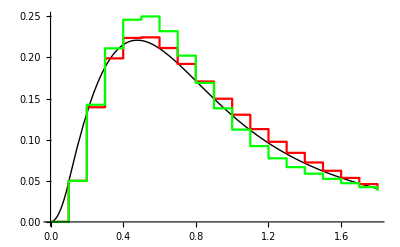
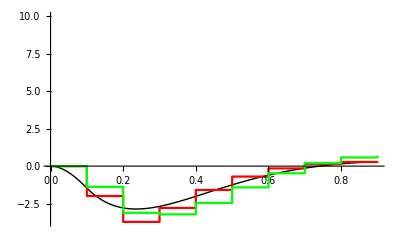
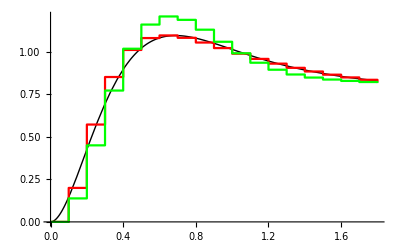
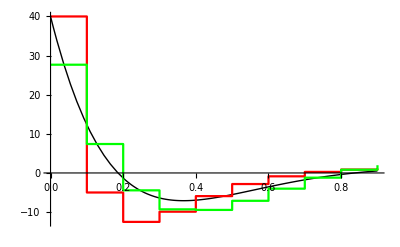

```mathematica
G1dtf =  ToDiscreteTimeModel[G1tf,Ts,z,Method -> "ZeroOrderHold"];
K1dtf = ToDiscreteTimeModel[K1tf,Ts,z,Method-> "ForwardRectangularRule"];
G1d=Divide@@G1dtf[[1]];  K1d=Divide@@K1dtf[[1]]; 
S1d=Together[1/(1+G1d K1d)];  T1d=Together[1-S1d]; GS1d= Together[G1d S1d]; KS1d=Together[K1d S1d];

K1adtf = ToDiscreteTimeModel[K1tf,Ts,z,Method-> "BilinearTransform"];
K1ad=Divide@@K1adtf[[1]];
S1ad=Together[1/(1+G1d K1ad)];  T1ad=Together[1-S1ad]; GS1ad= Together[G1d S1ad];
KS1ad= Together[K1ad S1ad];

T1dtf=TransferFunctionModel[T1d,z,SamplingPeriod->Ts];
GS1dtf=TransferFunctionModel[GS1d,z,SamplingPeriod->Ts];
KS1dtf=TransferFunctionModel[KS1d,z,SamplingPeriod->Ts];

T1adtf=TransferFunctionModel[T1ad,z,SamplingPeriod->Ts];
GS1adtf=TransferFunctionModel[GS1ad,z,SamplingPeriod->Ts];
KS1adtf=TransferFunctionModel[KS1ad,z,SamplingPeriod->Ts];

y1d=OutputResponse[GS1dtf,DiscreteImpulse,{t,0,tmax}][[1]]  (* Euler *);     
u1d=-OutputResponse[T1dtf,DiscreteImpulse,{t,0,tmaxu}][[1]]  (* disturb *);
y1ad=OutputResponse[GS1adtf,DiscreteImpulse,{t,0,tmax}][[1]] (* Tustin *);
u1ad=-OutputResponse[T1adtf,DiscreteImpulse,{t,0,tmaxu}][[1]] (* disturb *);
y1dr=OutputResponse[T1dtf,UnitStep[t],{t,0,tmax}][[1]]   (* Euler, step *);
u1dr=OutputResponse[KS1dtf,UnitStep[t],{t,0,tmaxu}][[1]]; 
y1adr=OutputResponse[T1adtf,UnitStep[t],{t,0,tmax}][[1]]  (* Euler *);     
u1adr=OutputResponse[KS1adtf,UnitStep[t],{t,0,tmaxu}][[1]]; 

py1d=ListPlot[y1d,DataRange->{0,tmax},PlotStyle ->Red];
pu1d=ListPlot[u1d,DataRange->{0,tmaxu},PlotStyle ->Red];
py1ad=ListPlot[y1ad,DataRange->{0,tmax},PlotStyle ->Green];
pu1ad=ListPlot[u1ad,DataRange->{0,tmaxu},PlotStyle ->Green];
py1dr=ListPlot[y1dr,DataRange->{0,tmax},PlotStyle ->Red];
pu1dr=ListPlot[u1dr,DataRange->{0,tmaxu},PlotStyle ->Red];
py1adr=ListPlot[y1adr,DataRange->{0,tmax},PlotStyle ->Green];
pu1adr=ListPlot[u1adr,DataRange->{0,tmaxu},PlotStyle ->Green];

{Show[py1,py1d,py1ad],Show[puin,pu1,pu1d,pu1ad],Show[py1r,py1dr,py1adr],Show[pu1r,pu1dr,pu1adr]}
```

```mathematica
{K1,K1d,K1ad}
```

{(3+4 s)/(1+s/10),{{(1. (-37.+40. z))/z}},{{(-7.7+8.3 z)/(-0.1+0.3 z)}}}

Conclusions:  
Left:  Continuous (black) is better than Tustin (green) is better than Euler (red) for rejecting disturbances.

Middle:  The finite Ts limits controller action:  cont > Tustin > Euler
if Tf=0 (improper controller), Tustin has osc. pole  but is ok for Tf>0

Right:  The continuous controller is not so good at reference tracking.  
Can improve with feedforward (for a different problem!).   
Alternatively---but with some performance trade offs---we can use integral control.

Now try direct digital control (designing in z plane)  [Ex. 2]

```mathematica
Ng = Numerator[G1d];Dg=Denominator[G1d]; Nz=n0+n1 z+n2 z^2; Dz=1+d1 z+d2 z^2;
Eqz=Together[Nz Ng+ Dz Dg - (z-0.0)^4];Eqsol=SolveAlways[{Eqz==0},z]
```

{{d2→1.,n0→-200.167,d1→1.74937,n1→248.334,n2→48.167}}

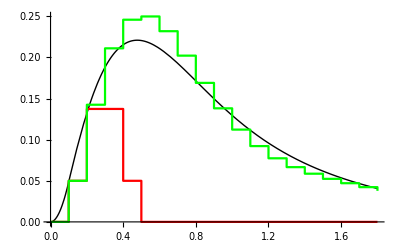
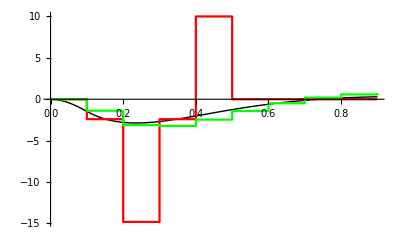
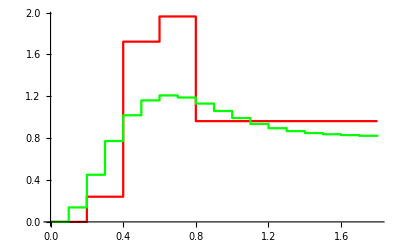
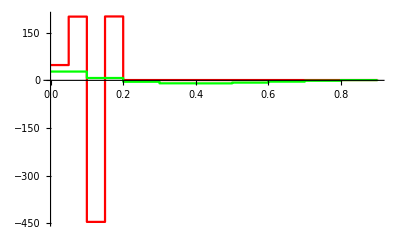

```mathematica
K2d=Nz/Dz/.Eqsol[[1]];  (* the synthesized controller *)
S2d=Chop[Together[1/(1+G1d K2d)]]; T2d=Together[1-S2d]; GS2d=Together[G1d S2d];
KS2d=Together[K2d S2d];

T2dtf=TransferFunctionModel[T2d,z,SamplingPeriod->Ts];
GS2dtf=TransferFunctionModel[GS2d,z,SamplingPeriod->Ts];
KS2dtf=TransferFunctionModel[KS2d,z,SamplingPeriod->Ts];

y2d=OutputResponse[GS2dtf,DiscreteDelta[t]/Ts,{t,0,tmax}][[1]];  (* input dist *)
u2d=-OutputResponse[T2dtf,DiscreteDelta[t]/Ts,{t,0,tmaxu}][[1]]; (* cont sig *)
y2ad=OutputResponse[T2dtf,UnitStep[t],{t,0,tmaxu}][[1]]; (* ref response *)
u2ad=OutputResponse[KS2dtf,UnitStep[t],{t,0,tmax}][[1]]; (* step 2 in *)

py2d=ListPlot[y2d,DataRange->{0,tmax},PlotStyle ->Red];
pu2d=ListPlot[u2d,DataRange->{0,tmaxu},PlotStyle ->Red];
py2ad=ListPlot[y2ad,DataRange->{0,tmax},PlotStyle ->Red];
pu2ad=ListPlot[u2ad,DataRange->{0,tmaxu},PlotStyle ->Red];

{Show[py1,py2d,py1ad],Show[puin,pu1,pu2d,pu1ad],Show[py2ad,py1adr],Show[pu2ad,pu1adr]}
```

Find state-space representations

```mathematica
{GS1ss=StateSpaceModel[GS1tf], T1ss=StateSpaceModel[T1tf],KS1ss=StateSpaceModel[KS1tf]}  (* continuous system *)
```

{01000010-40-41-10110100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,01000010-40-41-101304000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,01000010-40-41-101-1570-1600-37040StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
{GS1dss=StateSpaceModel[GS1dtf], T1dss=StateSpaceModel[T1dtf],KS1dss=StateSpaceModel[KS1dtf]}  (* Forward Euler *)
```

{01.0.000.1.00.184846-1.014991.790171.00.004995830.0049958300.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,01.0.000.1.00.184846-1.014991.790171.-0.1848460.01498750.19983300.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,01.0.000.1.00.184846-1.014991.790171.-29.606273.0308-44.993340.0.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
{GS1adss=StateSpaceModel[GS1adtf], T1adss=StateSpaceModel[T1adtf],KS1adss=StateSpaceModel[KS1adtf]}  (* Tustin *)
```

{01.0.000.1.00.46156-1.673332.185121.-0.001665280.003330560.0049958300.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,01.0.000.1.00.46156-1.673332.185121.-0.1282260.009991670.13821800.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic,01.0.000.1.00.46156-1.673332.185121.-12.896832.4481-20.268527.66670.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic}